```mathematica
t=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-a-test-n.wdx"];
m=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-a-n.wdx"];
```

```mathematica
f1t=Query[1,1]@t;
f1m=Query[1,1]@m;
```

```mathematica
pf1t=Interpolation[Flatten[f1t,1]];
pf1m=Interpolation[Flatten[f1m,1]];
```

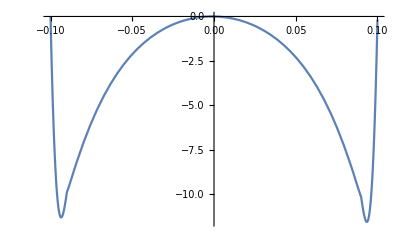

```mathematica
Plot[pf1t[x,-1],{x,-0.1,0.1}]
```

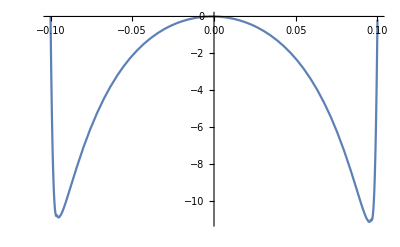

```mathematica
Plot[pf1m[x,-1],{x,-0.1,0.1}]
```

```mathematica
test[x_,y_]=pf1m[x,y]-pf1t[x,y];
```

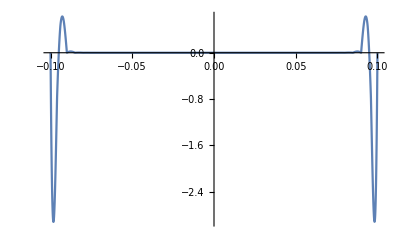

```mathematica
Plot[test[x,-1],{x,-0.1,0.1},PlotRange->All]
```

```mathematica
f2t=Query[2,1]@t;
f2m=Query[2,1]@m;
```

```mathematica
pf2t=Interpolation[Flatten[f2t,1]];
pf2m=Interpolation[Flatten[f2m,1]];
```

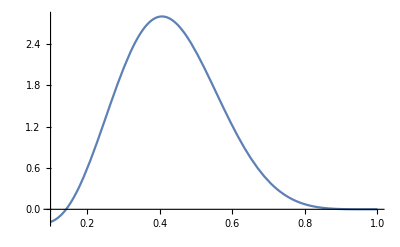

```mathematica
Plot[pf2t[x,-1],{x,0.1,1}]
```

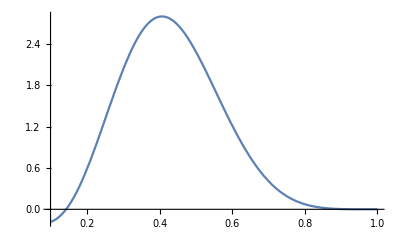

```mathematica
Plot[pf2m[x,-1],{x,0.1,1}]
```

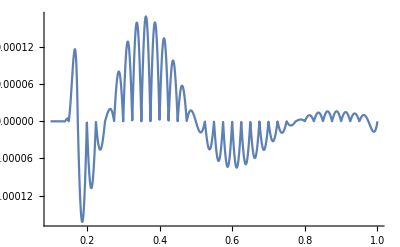

```mathematica
test2[x_,y_]=pf2m[x,y]-pf2t[x,y];
Plot[test2[x,-1],{x,0.1,1},PlotRange->All]
```